## Illustrate system of 1d ODEs as a flow in a vector field based on van der Pol equation (Sec. 11.1.5)

```mathematica
Clear["Global`*"];
```

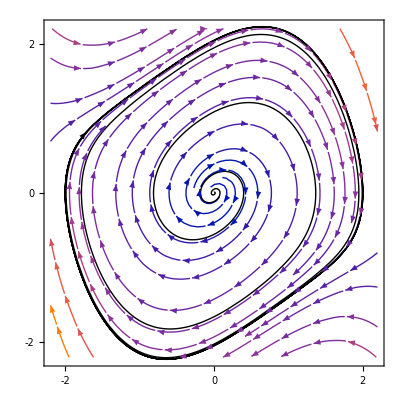

```mathematica
tend=50;
{x1sol,x2sol}=NDSolveValue[{
x1'[t]==x2[t], 
x2'[t]==-x1[t]+ϵ (1-x1[t]^2)x2[t],
x1[0]==0,
x2[0]==0.01}/.ϵ->0.5,{x1,x2},{t,0,tend}];
p1=ParametricPlot[{x1sol[t],x2sol[t]},{t,0,tend},PlotStyle->{Black,Thick}];
arrowPositions={{0.05,0.06},{0.05,0.11},{0.05,0.15},{0.05,0.575}};
p1a=p1/.Line[x_]:>{Arrowheads[arrowPositions],Arrow[x]};
p2=StreamPlot[{x2,-x1+ϵ (1-x1^2)x2}/.ϵ->0.5,{x1,-2.2,2.2},{x2,-2.2,2.2},StreamStyle->GrayLevel[0.65],StreamScale->0.1,StreamPoints->15,LabelStyle->{FontSize->30,FontFamily->"GillSans",Gray},
FrameTicks->{{{-2,0,2},None},{{-2,0,2},None}}];
pall=Show[p2,p1a,PlotRange->All]
```

Export data

```mathematica
(* 
SetDirectory[NotebookDirectory[]];Export["flowfield0.pdf",pall,Background->None] 
*)
```